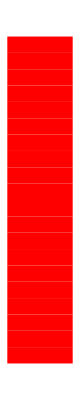

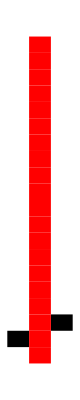

```mathematica
rectangles:=Table[{Red,Rectangle[{1,i-1}]},{i,1,20}]
(*AppendTo[rectangles,{Red,Rectangle[{0,0}]}]*)
(*AppendTo[rectangles,{Green,Rectangle[{0,0}]}*)

Graphics@rectangles
Show[Graphics[{Rectangle[{0,1}],Rectangle[{2,2}]}],Graphics@rectangles]
```